## AME (4, 6) Chess Constructor Wojciech Bruzda, Grzegorz Rajchel-Mieldzioć @ 2022/04/01 https://github.com/matrix-toolbox/

### autosave

```mathematica
StartScheduledTask[CreateScheduledTask[FrontEndExecute[FrontEndToken["Save"]],60]];
```

### possible LaTeX visualization

```mathematica
img1=Import["https://chaos.if.uj.edu.pl/~wojtek/AME46_chess/AME46_chess.png"];
Image[img1,Magnification->0.7]
```

-Graphics-

### aux. functions

```mathematica
S=ArrayFlatten[Transpose[ArrayReshape[IdentityMatrix[36],{6,6,6,6}],{3,1,2,4}]];

PartialTranspose[a_]:=Module[{dim,sdim,ret},
dim=Dimensions[a]⟦1⟧;
sdim=Sqrt[dim];
ret=Partition[a,{sdim,sdim}];
ret=Map[Transpose,ret,{2}];
ret=ArrayFlatten[ret];
Return[ret];
];

(* R2[M_]:=ArrayFlatten@Array[M⟦#2+d#1-d,#4+d#3-d⟧&,{d,d,d,d}] *)
Reshuffle[M_]:=Module[{d,ret},
d=Sqrt@Dimensions[M]⟦1⟧;
ret=ArrayFlatten@Array[M⟦#2+d#1-d,#4+d#3-d⟧&,{d,d,d,d}];
Return[ret]
];

SL[M_]:=Module[{d,ret},(* "linear" entropy *)
d=Sqrt@Dimensions[M]⟦1⟧;
ret=d^2/(d^2-1)(1-Total[Eigenvalues[M.M†]^2]/Tr[M.M†]^2);
Return[ret];
]

ep[M_]:=(SL[Reshuffle[M]]+SL[Reshuffle[M.S]]-1)//N
gt[M_]:=(SL[Reshuffle[M]]-SL[Reshuffle[M.S]]+1)//N

IndexOf[indices_,subdims_]:=Sequence@@(1+Reverse[#1-1].Most[FoldList[Times,1,Reverse[subdims]]]&)/@Transpose[Partition[indices,2]]
MatrixReshape[(matrix_)?SquareMatrixQ,subdims_]:=Array[matrix[[IndexOf[{##1},subdims]]]&,Riffle[subdims,subdims]]/;Times@@subdims==Length[matrix]
PartialTrace[(matrix_)?SquareMatrixQ,subdims_,(which_)?IntegerQ]:=NestWhile[ArrayFlatten,Map[Tr[#1,Plus,2]&,MatrixReshape[matrix,subdims],{2*which-2}],Length[Dimensions[#1]]>2&]/;Times@@subdims==Length[matrix]&&1≤which≤Length[subdims]

(*PartialTranspose[(matrix_)?SquareMatrixQ,subdims_,(which_)?IntegerQ]:=NestWhile[ArrayFlatten,Transpose[MatrixReshape[matrix,subdims],2*which-1<->2*which],Length[Dimensions[#1]]>2&]/;Times@@subdims==Length[matrix]&&1≤which≤Length[subdims]
*)
```

### AME(4, 6) state

```mathematica
w=Exp[(ⅈ π)/10];
c=1/(√2);
a=c/(w+Conjugate[w]);(*1/2 √(1-1/(√5))*)
b=c/(w^3+Conjugate[w]^3);(*1/2 √(1+1/(√5))*)
AME46FromPRL=({{0, c, 0, 0, 0, 0, c, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, c w^17, 0, 0, 0, 0, 0, 0, c w^19, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, a w^18, b w^3, 0, 0, 0, 0, b w^3, a w^18}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, a w^3, b, 0, 0, 0, 0, b, a w^7, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, b, a w^5, 0, 0, 0, 0, a w^5, b, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, b w^14, a w, 0, 0, 0, 0, a w^15, b w^12, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, c, 0, 0, 0, 0, c w^10, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, c w^7, 0, 0, 0, 0, 0, 0, c w^19, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, a w^2, b w^19, 0, 0, 0, 0, b w^13, a, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, c w^10, 0, 0, 0, 0, 0, 0, c w^6, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, a w^2, b w, 0, 0, 0, 0, b w^5, a w^14, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, b w^4, a w^3, 0, 0, 0, 0, a w^9, b w^18, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, c w^8, 0, 0, 0, 0, 0, 0, c w^16, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, c w^2, 0, 0, 0, 0, c w^2, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, c w^5, 0, 0, 0, 0, c w^19, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, a w, b w^10, 0, 0, 0, 0, b w^4, a w^3, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, c w^13, 0, 0, 0, 0, 0, 0, c w^7, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, a w^12, b w^15, 0, 0, 0, 0, b w, a w^14, 0, 0}, {0, 0, 0, 0, a w, b w^14, 0, 0, 0, 0, b w^16, a w^19, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {b w^10, a w^5, 0, 0, 0, 0, a w^15, b, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, b w^14, a w^7, 0, 0, 0, 0, a w^13, b w^16, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, b w^10, a w^5, 0, 0, 0, 0, a w^5, b w^10}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, a w^4, b w^17, 0, 0, 0, 0, b w^7, a w^10, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, a, b w^15, 0, 0, 0, 0, b w^15, a, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, c w^14, 0, 0, 0, 0, c w^10, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, c, 0, 0, 0, 0, c w^10, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, b w^7, a w^10, 0, 0, 0, 0, a, b w^13, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, c, 0, 0, 0, 0, 0, 0, c w^10, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, b w^2, a w^5, 0, 0, 0, 0, a w^15, b w^8, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {c, 0, 0, 0, 0, 0, 0, c, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, c, 0, 0, 0, 0, c w^10, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, c w^16, 0, 0, 0, 0, c, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {a w^10, b w^15, 0, 0, 0, 0, b w^5, a, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, b w^14, a w^3, 0, 0, 0, 0, a w^7, b w^6, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, c w, 0, 0, 0, 0, 0, 0, c w^11}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, b w^9, a w^16, 0, 0, 0, 0, a w^16, b w^13, 0, 0, 0, 0}});

U=PartialTranspose[AME46FromPRL];
On[Assert]
Assert[ep@N@U==1]
Assert[gt@N@U==1]
Off[Assert]
```

### relation of "new" U that resembles OLS(3) to the original matrix from the PRL

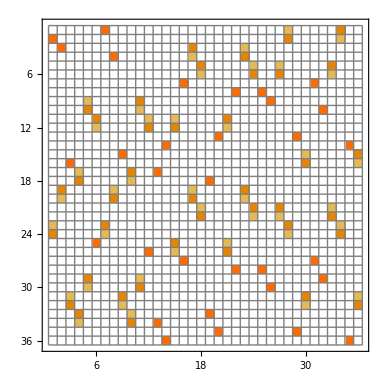
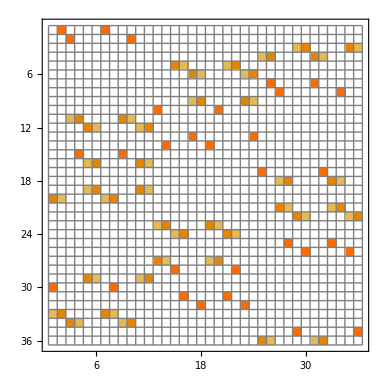

```mathematica
PRL=PartialTranspose[U];

MatrixPlot[#,Mesh->All,PlotTheme->"Default",
FrameStyle->Opacity[1],
MeshStyle->Directive[Gray],
FrameTicksStyle->Directive[Black,22],
FrameTicks->{{6,12,18,24,30,36},{6,12,18,24,30,36}},
ImageSize->384]&/@Abs@{U,PRL}
```

### three forms of AME46 in matrix plot

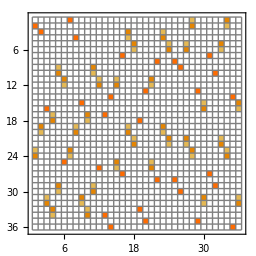
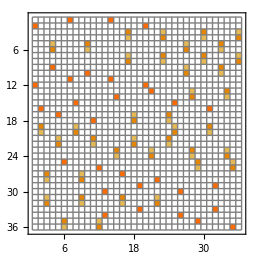
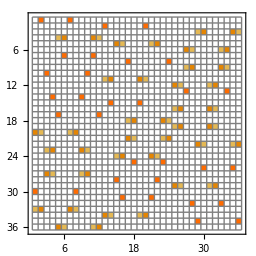
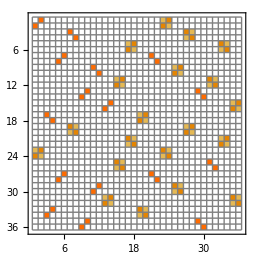
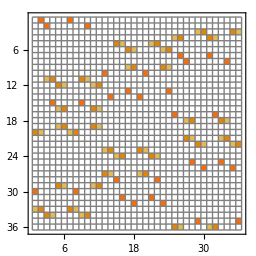
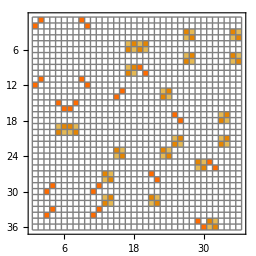
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* there are (6!)^4 = 268'738'560'000 other possibile forms that can be found using local permutation matrices of order six *)
MatrixPlot[#,Mesh->All,PlotTheme->"Default",
FrameStyle->Opacity[1],
MeshStyle->Directive[Gray],
FrameTicksStyle->Directive[Black,22],
FrameTicks->{{6,12,18,24,30,36},{6,12,18,24,30,36}},
ImageSize->256]&/@Abs@{
U,
Reshuffle[U],
PartialTranspose[Reshuffle[U]],
Reshuffle[PartialTranspose[Reshuffle[U]]],
PartialTranspose[U],
Reshuffle[PartialTranspose[U]],
PartialTranspose[Reshuffle[PartialTranspose[U]]] 
}
```

### chess representation of AME(4, 6)

```mathematica
V=PartialTranspose[Reshuffle[PartialTranspose[U]]];
(* 1st six columns for King *)
(* 2nd six columns for Queen, and then: kNight, Bishop, Rook, and Pawn *)
(* 1st column is red, 2nd - cyan, and then: green, magenta, blue, and yellow; and they repeat cyclically... *)
ChessFig =<|0->"K",1->"Q",2->"N",3->"B",4->"R",5->"P"|>;
ChessCol=<|0->"r",1->"c",2->"g",3->"m",4->"b",5->"y"|>;
ChessSize=<|1/(√2)->"B",1/2 √(1+1/(√5))->"M",1/(√(5+√5))->"S"|>;(* Big, Medium, Small... *)
MM=ConstantArray[0,{36,36}];
For[r=1,r<=36,r++,
For[c=1,c<=36,c++,
If[V⟦r,c⟧==0,MM⟦r,c⟧=".",MM⟦r,c⟧={ChessFig[Floor[(c-1)/6]],ChessCol[Mod[(c-1),6]],Mod[(20Pi+Arg[V⟦r,c⟧]*10)*Unitize[Arg[V⟦r,c⟧]],20Pi]/Pi,ChessSize[FullSimplify[Abs[V⟦r,c⟧]]]}//FullSimplify]
]]
(* MM//MatrixForm *)

ChessBoard=ConstantArray[0,{6,6}];
For[j=1,j<=36,j++,
ChessBoard⟦Floor[(j-1)/6]+1,Mod[j-1,6]+1⟧=DeleteCases[MM⟦j⟧,"."]
]
ChessBoard
readyForJS=StringReplace[ToString[%],{"{"->"[","}"->"]",
"K"->"'K'","Q"->"'Q'","N"->"'N'","B"->"'B'","R"->"'R'","P"->"'P'",
"r"->"'r'","c"->"'c'","g"->"'g'","m"->"'m'","b"->"'b'","y"->"'y'",
"S"->"'S'","M"->"'M'","B"->"'B'"}]
```

{{{{K,c,0,B},{B,b,3,S},{B,y,0,M}},{{K,r,0,B},{B,b,0,M},{B,y,7,S}},{{Q,r,17,B},{R,g,0,M},{R,m,5,S}},{{Q,c,19,B},{R,g,5,S},{R,m,0,M}},{{N,b,18,S},{N,y,3,M},{P,g,14,M},{P,m,15,S}},{{N,b,3,M},{N,y,18,S},{P,g,1,S},{P,m,12,M}}},{{{K,y,10,B},{B,g,10,B}},{{K,b,0,B},{B,m,6,B}},{{Q,b,7,B},{R,r,2,S},{R,c,5,M}},{{Q,y,19,B},{R,r,1,M},{R,c,14,S}},{{N,g,2,S},{N,m,13,M},{P,r,4,M},{P,c,9,S}},{{N,g,19,M},{N,m,0,S},{P,r,3,S},{P,c,18,M}}},{{{Q,m,2,B},{R,b,13,B}},{{Q,g,2,B},{R,y,7,B}},{{N,c,19,B},{P,b,12,S},{P,y,1,M}},{{N,r,5,B},{P,b,15,M},{P,y,14,S}},{{K,g,8,B},{B,r,1,S},{B,c,4,M}},{{K,m,16,B},{B,r,10,M},{B,c,3,S}}},{{{Q,r,10,M},{Q,c,15,S},{R,g,4,S},{R,m,7,M}},{{Q,r,5,S},{Q,c,0,M},{R,g,17,M},{R,m,10,S}},{{N,b,14,M},{N,y,13,S},{P,g,0,S},{P,m,15,M}},{{N,b,7,S},{N,y,16,M},{P,g,15,M},{P,m,0,S}},{{K,r,1,S},{K,c,16,M},{B,b,10,M},{B,y,5,S}},{{K,r,14,M},{K,c,19,S},{B,b,5,S},{B,y,10,M}}},{{{N,g,7,M},{N,m,0,S},{P,r,0,B}},{{N,g,10,S},{N,m,13,M},{P,c,0,B}},{{K,y,10,B},{B,g,0,B}},{{K,b,14,B},{B,m,10,B}},{{Q,y,10,B},{R,r,2,M},{R,c,15,S}},{{Q,b,0,B},{R,r,5,S},{R,c,8,M}}},{{{N,r,10,S},{N,c,5,M},{P,b,9,M},{P,y,16,S}},{{N,r,15,M},{N,c,0,S},{P,b,16,S},{P,y,13,M}},{{K,m,10,B},{B,r,14,M},{B,c,7,S}},{{K,g,0,B},{B,r,3,S},{B,c,6,M}},{{Q,m,0,B},{R,b,1,B}},{{Q,g,16,B},{R,y,11,B}}}}

[[[['K', 'c', 0, 'B'], ['B', 'b', 3, 'S'], ['B', 'y', 0, 'M']], [['K', 'r', 0, 'B'], ['B', 'b', 0, 'M'], ['B', 'y', 7, 'S']], [['Q', 'r', 17, 'B'], ['R', 'g', 0, 'M'], ['R', 'm', 5, 'S']], [['Q', 'c', 19, 'B'], ['R', 'g', 5, 'S'], ['R', 'm', 0, 'M']], [['N', 'b', 18, 'S'], ['N', 'y', 3, 'M'], ['P', 'g', 14, 'M'], ['P', 'm', 15, 'S']], [['N', 'b', 3, 'M'], ['N', 'y', 18, 'S'], ['P', 'g', 1, 'S'], ['P', 'm', 12, 'M']]], [[['K', 'y', 10, 'B'], ['B', 'g', 10, 'B']], [['K', 'b', 0, 'B'], ['B', 'm', 6, 'B']], [['Q', 'b', 7, 'B'], ['R', 'r', 2, 'S'], ['R', 'c', 5, 'M']], [['Q', 'y', 19, 'B'], ['R', 'r', 1, 'M'], ['R', 'c', 14, 'S']], [['N', 'g', 2, 'S'], ['N', 'm', 13, 'M'], ['P', 'r', 4, 'M'], ['P', 'c', 9, 'S']], [['N', 'g', 19, 'M'], ['N', 'm', 0, 'S'], ['P', 'r', 3, 'S'], ['P', 'c', 18, 'M']]], [[['Q', 'm', 2, 'B'], ['R', 'b', 13, 'B']], [['Q', 'g', 2, 'B'], ['R', 'y', 7, 'B']], [['N', 'c', 19, 'B'], ['P', 'b', 12, 'S'], ['P', 'y', 1, 'M']], [['N', 'r', 5, 'B'], ['P', 'b', 15, 'M'], ['P', 'y', 14, 'S']], [['K', 'g', 8, 'B'], ['B', 'r', 1, 'S'], ['B', 'c', 4, 'M']], [['K', 'm', 16, 'B'], ['B', 'r', 10, 'M'], ['B', 'c', 3, 'S']]], [[['Q', 'r', 10, 'M'], ['Q', 'c', 15, 'S'], ['R', 'g', 4, 'S'], ['R', 'm', 7, 'M']], [['Q', 'r', 5, 'S'], ['Q', 'c', 0, 'M'], ['R', 'g', 17, 'M'], ['R', 'm', 10, 'S']], [['N', 'b', 14, 'M'], ['N', 'y', 13, 'S'], ['P', 'g', 0, 'S'], ['P', 'm', 15, 'M']], [['N', 'b', 7, 'S'], ['N', 'y', 16, 'M'], ['P', 'g', 15, 'M'], ['P', 'm', 0, 'S']], [['K', 'r', 1, 'S'], ['K', 'c', 16, 'M'], ['B', 'b', 10, 'M'], ['B', 'y', 5, 'S']], [['K', 'r', 14, 'M'], ['K', 'c', 19, 'S'], ['B', 'b', 5, 'S'], ['B', 'y', 10, 'M']]], [[['N', 'g', 7, 'M'], ['N', 'm', 0, 'S'], ['P', 'r', 0, 'B']], [['N', 'g', 10, 'S'], ['N', 'm', 13, 'M'], ['P', 'c', 0, 'B']], [['K', 'y', 10, 'B'], ['B', 'g', 0, 'B']], [['K', 'b', 14, 'B'], ['B', 'm', 10, 'B']], [['Q', 'y', 10, 'B'], ['R', 'r', 2, 'M'], ['R', 'c', 15, 'S']], [['Q', 'b', 0, 'B'], ['R', 'r', 5, 'S'], ['R', 'c', 8, 'M']]], [[['N', 'r', 10, 'S'], ['N', 'c', 5, 'M'], ['P', 'b', 9, 'M'], ['P', 'y', 16, 'S']], [['N', 'r', 15, 'M'], ['N', 'c', 0, 'S'], ['P', 'b', 16, 'S'], ['P', 'y', 13, 'M']], [['K', 'm', 10, 'B'], ['B', 'r', 14, 'M'], ['B', 'c', 7, 'S']], [['K', 'g', 0, 'B'], ['B', 'r', 3, 'S'], ['B', 'c', 6, 'M']], [['Q', 'm', 0, 'B'], ['R', 'b', 1, 'B']], [['Q', 'g', 16, 'B'], ['R', 'y', 11, 'B']]]]

### color matching in rows 1 and 2 of U

```mathematica
rf12=c c w^(0-10)QrPr+c c w^(0-0)KrRr//N
cf12=c c w^(17-7)KcRc+c c w^(19-19)QcPc//N
```

0.5 KrRr-0.5 QrPr

-0.5 KcRc+0.5 QcPc

```mathematica
gf12=a a w^(18-2)RgNg+a b w^(18-13)RgBg+b a w^(3-2)PgNg+b b w^(3-13)PgBg+b b w^(3-19)RgNg+b a w^(3-0)RgBg+a b w^(18-19)PgNg+a a w^(18-0)PgBg//N
mf12=b c w^(0-10)PmNm+a c w^(3-10)RmNm+a c w^(7-6)PmBm+b c w^(0-6)RmBm//N
```

(-0.25-0.0812299 ⅈ) PgBg+(0.425325+0. ⅈ) PgNg+(0.131433+0.404508 ⅈ) RgBg+(0.154508+0.212663 ⅈ) RgNg

(0.25+0.0812299 ⅈ) PmBm-(0.425325+0. ⅈ) PmNm-(0.131433+0.404508 ⅈ) RmBm-(0.154508+0.212663 ⅈ) RmNm

```mathematica
bf12=a a w^(5-2)BbKb +a b w^(5-5)BbQb+b a w^(0-2)NbKb+b b w^(0-5)NbQb+b b w^(0-1)BbKb+b a w^(0-14)BbQb+a b w^(5-1)NbKb+a a w^(5-14)NbQb//N//Chop
yf12=b b w^(14-4)NyKy+b a w^(14-9)NyQy+a b w^(15-4)ByKy+a a w^(15-9)ByQy+a a w^(1-3)NyKy+a b w^(1-18)NyQy+b a w^(12-3)ByKy+b b w^(12-18)ByQy//N
```

0.425325 BbKb+(0.154508+0.212663 ⅈ) BbQb+(0.25+0.0812299 ⅈ) NbKb-(0.131433+0.404508 ⅈ) NbQb

(-0.425325+0. ⅈ) ByKy-(0.154508+0.212663 ⅈ) ByQy-(0.25+0.0812299 ⅈ) NyKy+(0.131433+0.404508 ⅈ) NyQy

### color matching in rows 3 and 4 of U

```mathematica
rf34=c a w^(8-1)NrKr+c b w^(8-16)NrQr+c b w^(16-14) BrKr + c a w^(16-19)BrQr//N
cf34=c b w^(2-10)BcKc + c a w^(2-15) BcQc + c a w^(2-5) NcKc + c b w^(2-0) NcQc//N
```

(0.344095+0.25 ⅈ) BrKr+(0.154508-0.212663 ⅈ) BrQr-(0.154508-0.212663 ⅈ) NrKr-(0.344095+0.25 ⅈ) NrQr

(-0.344095-0.25 ⅈ) BcKc-(0.154508-0.212663 ⅈ) BcQc+(0.154508-0.212663 ⅈ) NcKc+(0.344095+0.25 ⅈ) NcQc

```mathematica
gf34=c b w^(19-14) QgRg+c a w^(19-13) QgPg+c a w^(5-7)KgRg+ c b w^(5-16)KgPg//N
mf34=a b w^(1-10)KmRm+a a w^(1-5)KmPm+b b w^(4-10)QmRm +b a w^(4-5)QmPm+b a w^(10-5)KmRm+b b w^(10-10)KmPm+a a w^(3-5)QmRm+a b w^(3-10)QmPm//N//Chop
```

(-0.404508+0.131433 ⅈ) KgPg+(0.212663-0.154508 ⅈ) KgRg-(0.0812299-0.25 ⅈ) QgPg+(0.+0.425325 ⅈ) QgRg

(0.404508-0.131433 ⅈ) KmPm-(0.212663-0.154508 ⅈ) KmRm+(0.0812299-0.25 ⅈ) QmPm-(0.+0.425325 ⅈ) QmRm

```mathematica
bf34=c a w^(13-4)RbNb+c b w^(13-7)RbBb+c b w^(7-17) PbNb + c a w^(7-10)PbBb//N
yf34=b a w^(1-0) PyNy+b b w^(1-15)PyBy+a a w^(12-0) RyNy+a b w^(12-15)RyBy+a b w^(14-15)PyNy+a a w^(14-0)PyBy+b b w^(15-15)RyNy+b a w^(15-0)RyBy//N
```

(0.154508-0.212663 ⅈ) PbBb-(0.425325+0. ⅈ) PbNb-(0.131433-0.404508 ⅈ) RbBb-(0.25-0.0812299 ⅈ) RbNb

(-0.154508+0.212663 ⅈ) PyBy+(0.425325+0. ⅈ) PyNy+(0.131433-0.404508 ⅈ) RyBy+(0.25-0.0812299 ⅈ) RyNy

### color matching in rows 5 and 6 of U

```mathematica
rf56=c c w^(10-10)PrBr+c c w^(14-0)RrNr//N
cf56=c c w^(10- 0)PcBc+c c w^(0-16)RcNc//N
```

0.5 PrBr-(0.154508+0.475528 ⅈ) RrNr

-0.5 PcBc+(0.154508+0.475528 ⅈ) RcNc

```mathematica
gf56=a a w^(0-10)BgKg+a b w^(0-5)BgQg+b a w^(7-10)NgKg+b b w^(7-5)NgQg+b b w^(13-15)BgKg+b a w^(13-0)BgQg+a b w^(10-15)NgKg+a a w^(10-0)NgQg//N
mf56=c b w^(0-14)NmKm+c a w^(0-7)NmQm+c a w^(10-3)BmKm+c b w^(10-6)BmQm//N
```

(0.154508-0.212663 ⅈ) BgKg-(0.131433+0.404508 ⅈ) BgQg+(0.131433-0.404508 ⅈ) NgKg+(0.154508+0.212663 ⅈ) NgQg

(-0.154508+0.212663 ⅈ) BmKm+(0.131433+0.404508 ⅈ) BmQm-(0.131433-0.404508 ⅈ) NmKm-(0.154508+0.212663 ⅈ) NmQm

```mathematica
bf56=b c w^(2-1)KbRb+a c w^(15-1)QbRb+a c w^(5-11)KbPb+b c w^(8-11)QbPb//N
yf56=c b w^(0-9)KyRy+c a w^(0-16)KyPy+c a w^(0-16)QyRy+c b w^(0-13)QyPy//N
```

(-0.0812299-0.25 ⅈ) KbPb+(0.404508+0.131433 ⅈ) KbRb+(0.25-0.344095 ⅈ) QbPb-(0.0812299+0.25 ⅈ) QbRb

(0.0812299+0.25 ⅈ) KyPy-(0.404508+0.131433 ⅈ) KyRy-(0.25-0.344095 ⅈ) QyPy+(0.0812299+0.25 ⅈ) QyRy

### figures matching in columns 1 and 2 of U

```mathematica
(* Bishop and kNight *)
BcNc=1; (* assign one to each projector to simulate Partial Trace... *)
BbNb=1;
BgNg=1;
BishopAndKnight=c c w^(2-2)BcNc+b b w^(7-17)BbNb+a a w^(0-10)BgNg//N//Chop
```

0

```mathematica
(* kNight and Bishop (they do not "commute"! *)
NmBm=1;
NbBb=1;
NgBg=1;
NightAndBishop=c c w^(10-6)NmBm+a a w^(4-10)NbBb+b b w^(7-13)NgBg//N//Chop
```

0

```mathematica
(* Queen and King *)
QrKr=1;
QcKc=1;
QgKg=1;
QueenAndKing=c c w^(0-0)QrKr+a a w^(15-5)QcKc+b b w^(5-15)QgKg//N//Chop
```

0

```mathematica
(* King and Queen *)
KcQc=1;
KyQy=1;
KgQg=1;
KingAndQueen=b b w^(10-0)KcQc+c c w^(0-0)KyQy+a a w^(10-0)KgQg//N//Chop
```

0

```mathematica
(* Rook and Pawn *)
RmPm=1;
RbPb=1;
RyPy=1;
RookAndPawn=a a w^(3-7)RmPm+c c w^(13-7)RbPb+b b w^(9-13)RyPy//N//Chop
```

0

```mathematica
(* Pawn and Rook *)
PmRm=1;
PbRb=1;
PyRy=1;
PawnAndRook=b b w^(0-0)PmRm+c c w^(10-0)PbRb+a a w^(16-16)PyRy//N//Chop
```

0